### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={200,500,500}; (*мощности слоев*)
slopes = {0 Degree, 0.9 Degree, -0.3 Degree, -4 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)

type = 1 ;
listV = {2000,2000,2000,2000}; (*набор скоростей*)
```

```mathematica
velocityTrend = 0;(*1 or 0*)
velocityAnomaly =0; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "regular"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["horizons"]];
table = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]]
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
optsVel1 = {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
							ImageSize -> 500};
optsVel2 = {ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 20}(*,
					GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None}*)};
PlotVelocity[velModel, horizons,{optsVel1, optsVel2}]
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

```mathematica
|
```

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[-1196.19+3450.49 t],FittedModel[-857.787+2289.41 t],FittedModel[-196.727+1572.62 t]}

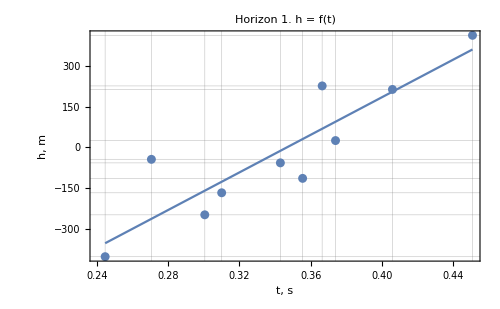
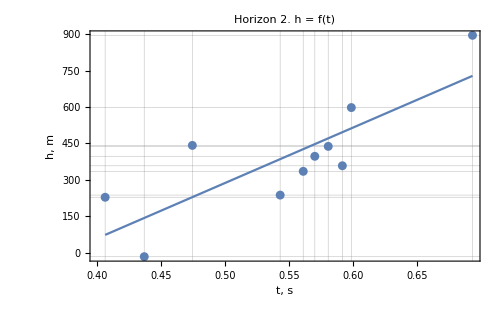
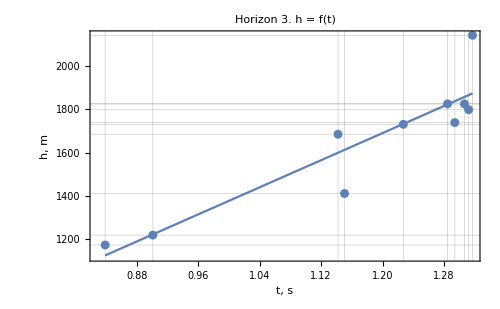

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[-3750.98+10514. t],FittedModel[-854.383+2819.04 t],FittedModel[1226.17+149.377 t]}

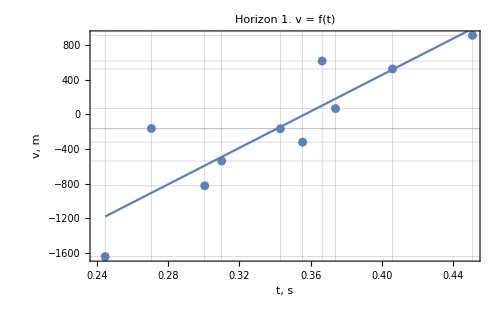
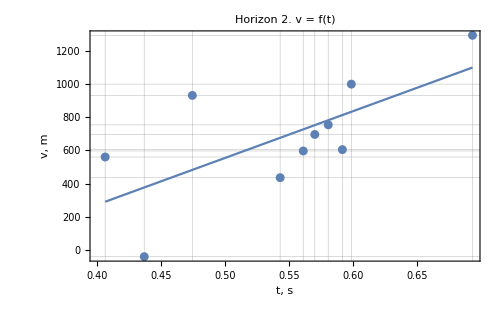
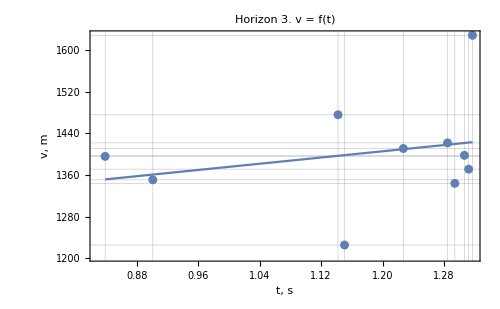

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[0.345696+0.000227307 h],FittedModel[0.43458+0.000283665 h],FittedModel[0.303674+0.000527964 h]}

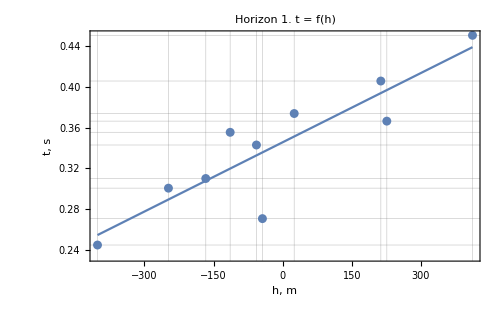
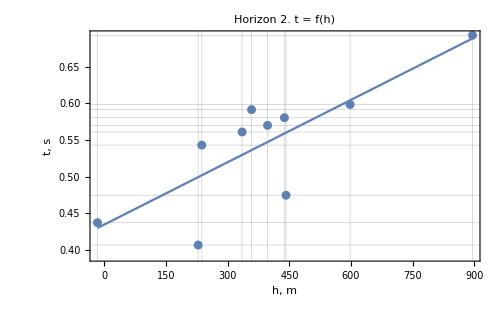
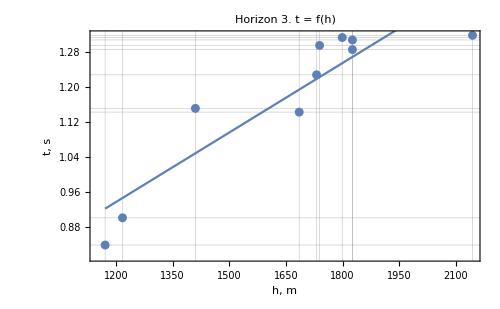

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{2000.,2000.,2000.}

{{{0,-570.},{100,-576.},{200,-583.},{300,-591.},{400,-601.},{500,-612.},{600,-622.},{700,-631.},{800,-639.},{900,-644.},{1000,-646.},{1100,-644.},{1200,-638.},{1300,-631.},{1400,-620.},{1500,-609.},{1600,-598.},{1700,-590.},{1800,-587.},{1900,-589.},{2000,-597.},{2100,-611.},{2200,-631.},{2300,-657.},{2400,-686.},{2500,-715.},{2600,-742.},{2700,-766.},{2800,-783.},{2900,-792.},{3000,-793.},{3100,-784.},{3200,-767.},{3300,-742.},{3400,-711.},{3500,-677.},{3600,-641.},{3700,-607.},{3800,-575.},{3900,-547.},{4000,-525.},{4100,-507.},{4200,-496.},{4300,-490.},{4400,-489.},{4500,-493.},{4600,-502.},{4700,-517.},{4800,-537.},{4900,-561.},{5000,-592.},{5100,-627.},{5200,-666.},{5300,-706.},{5400,-748.},{5500,-786.},{5600,-820.},{5700,-848.},{5800,-868.},{5900,-879.},{6000,-881.},{6100,-874.},{6200,-859.},{6300,-838.},{6400,-812.},{6500,-783.},{6600,-751.},{6700,-718.},{6800,-685.},{6900,-653.},{7000,-621.},{7100,-593.},{7200,-570.},{7300,-551.},{7400,-541.},{7500,-541.},{7600,-552.},{7700,-574.},{7800,-607.},{7900,-650.},{8000,-701.},{8100,-755.},{8200,-809.},{8300,-861.},{8400,-902.},{8500,-932.},{8600,-949.},{8700,-951.},{8800,-939.},{8900,-915.},{9000,-883.},{9100,-844.},{9200,-804.},{9300,-766.},{9400,-733.},{9500,-706.},{9600,-686.},{9700,-676.},{9800,-673.},{9900,-675.},{10000,-683.}},{{0,-1058.},{100,-1062.},{200,-1067.},{300,-1075.},{400,-1086.},{500,-1099.},{600,-1114.},{700,-1131.},{800,-1148.},{900,-1162.},{1000,-1171.},{1100,-1172.},{1200,-1164.},{1300,-1148.},{1400,-1122.},{1500,-1090.},{1600,-1055.},{1700,-1024.},{1800,-999.},{1900,-986.},{2000,-988.},{2100,-1006.},{2200,-1040.},{2300,-1087.},{2400,-1140.},{2500,-1196.},{2600,-1248.},{2700,-1293.},{2800,-1325.},{2900,-1344.},{3000,-1346.},{3100,-1329.},{3200,-1295.},{3300,-1245.},{3400,-1183.},{3500,-1113.},{3600,-1042.},{3700,-977.},{3800,-924.},{3900,-886.},{4000,-865.},{4100,-858.},{4200,-861.},{4300,-868.},{4400,-874.},{4500,-876.},{4600,-875.},{4700,-872.},{4800,-875.},{4900,-887.},{5000,-914.},{5100,-957.},{5200,-1015.},{5300,-1085.},{5400,-1161.},{5500,-1234.},{5600,-1297.},{5700,-1346.},{5800,-1375.},{5900,-1383.},{6000,-1371.},{6100,-1342.},{6200,-1299.},{6300,-1248.},{6400,-1197.},{6500,-1149.},{6600,-1107.},{6700,-1072.},{6800,-1043.},{6900,-1016.},{7000,-984.},{7100,-948.},{7200,-905.},{7300,-858.},{7400,-813.},{7500,-778.},{7600,-761.},{7700,-770.},{7800,-808.},{7900,-876.},{8000,-968.},{8100,-1078.},{8200,-1192.},{8300,-1299.},{8400,-1386.},{8500,-1443.},{8600,-1468.},{8700,-1456.},{8800,-1412.},{8900,-1342.},{9000,-1255.},{9100,-1163.},{9200,-1076.},{9300,-1003.},{9400,-949.},{9500,-917.},{9600,-906.},{9700,-913.},{9800,-931.},{9900,-955.},{10000,-981.}},{{0,-2581.},{100,-2599.},{200,-2612.},{300,-2596.},{400,-2588.},{500,-2579.},{600,-2572.},{700,-2604.},{800,-2633.},{900,-2675.},{1000,-2712.},{1100,-2743.},{1200,-2708.},{1300,-2666.},{1400,-2613.},{1500,-2565.},{1600,-2514.},{1700,-2456.},{1800,-2370.},{1900,-2288.},{2000,-2254.},{2100,-2244.},{2200,-2304.},{2300,-2445.},{2400,-2569.},{2500,-2679.},{2600,-2738.},{2700,-2759.},{2800,-2757.},{2900,-2760.},{3000,-2764.},{3100,-2763.},{3200,-2765.},{3300,-2695.},{3400,-2624.},{3500,-2513.},{3600,-2350.},{3700,-2162.},{3800,-2026.},{3900,-1945.},{4000,-1938.},{4100,-2007.},{4200,-2128.},{4300,-2209.},{4400,-2301.},{4500,-2275.},{4600,-2189.},{4700,-2086.},{4800,-1981.},{4900,-1901.},{5000,-1920.},{5100,-1986.},{5200,-2119.},{5300,-2279.},{5400,-2454.},{5500,-2546.},{5600,-2615.},{5700,-2647.},{5800,-2645.},{5900,-2661.},{6000,-2652.},{6100,-2622.},{6200,-2584.},{6300,-2458.},{6400,-2284.},{6500,-2137.},{6600,-2043.},{6700,-2030.},{6800,-2092.},{6900,-2172.},{7000,-2226.},{7100,-2219.},{7200,-2120.},{7300,-1960.},{7400,-1802.},{7500,-1699.},{7600,-1594.},{7700,-1564.},{7800,-1581.},{7900,-1672.},{8000,-1837.},{8100,-2064.},{8200,-2290.},{8300,-2481.},{8400,-2634.},{8500,-2711.},{8600,-2714.},{8700,-2670.},{8800,-2581.},{8900,-2461.},{9000,-2277.},{9100,-2085.},{9200,-1875.},{9300,-1746.},{9400,-1678.},{9500,-1649.},{9600,-1698.},{9700,-1798.},{9800,-1914.},{9900,-1948.},{10000,-1908.}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-